### Вспомогательные графики

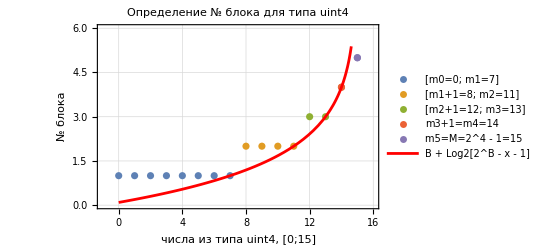

```mathematica
Show[ListPlot[{({#,1}&/@Range[0,7]),({#,2}&/@Range[8,11]),({#,3}&/@Range[12,13]),{#,4}&/@Range[14,14],{#,5}&/@Range[15,15]},PlotLegends->{"[m0=0; m1=7]","[m1+1=8; m2=11]","[m2+1=12; m3=13]","m3+1=m4=14","m5=M=2^4 - 1=15"},FrameLabel->{"числа из типа uint4, [0;15]","№ блока"},PlotTheme->"Detailed"],
Plot[4-Log2[2^4-x-1] ,{x,0,15},PlotStyle->Red,PlotLegends->{"B + Log2[2^B - x - 1]"}],PlotRange->{{-1,16},{0,6}},ImageSize->Scaled[0.8],PlotLabel->"Определение № блока для типа uint4"]
```

### Benhmark 1: Random Push

```mathematica
dataVec1 ={{524288,2113898,6736},{1048576,4200458,7550},{2097152,9356026,14318},{4194304,17767600,5529},{8388608,35197033,13765},{16777216,68962181,29852},{33554432,130399980,87485}};
dataStack1 = {{524288,5337908,23719},{1048576,10631407,59034},{2097152,21242136,91552},{4194304,42440964,217020},{8388608,91154957,141658},{16777216,179573653,608165},{33554432,312691975,1727248}};
dataStandardStack1 = {{524288,6546702,11681},{1048576,13227689,36355},{2097152,26177077,63088},{4194304,55501098,65173},{8388608,114545676,113684},{16777216,215928425,240397},{33554432,344566143,383090}};
```

```mathematica
lineVec1=Fit[{#[[1]],#[[2]]}&/@dataVec1,{1,x},x]
```

1.25436×10^6+3.89304 x

```mathematica
lineStack1=Fit[{#[[1]],#[[2]]}&/@dataStack1,{1,x},x]
```

4.85011×10^6+9.44847 x

```mathematica
lineStandardStack1=Fit[{#[[1]],#[[2]]}&/@dataStandardStack1,{1,x},x]
```

1.15678×10^7+10.4456 x

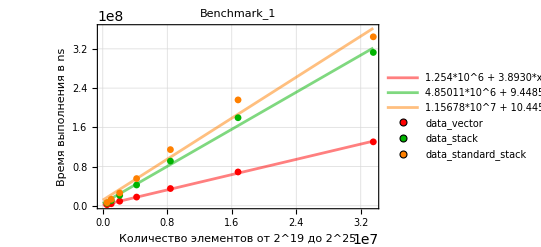

```mathematica
Show[
Plot[lineVec1,{x,0,dataVec1[[-1]][[1]]},PlotLegends->{"1.254*10^6 + 3.8930*x"},PlotStyle->Directive[Opacity[0.5],Red],PlotTheme->"Detailed"],
Plot[lineStack1,{x,0,dataStack1[[-1]][[1]]},PlotLegends->{"4.85011*10^6 + 9.4485*x"},PlotStyle->RGBColor[0,0.7,0,0.5]],
Plot[lineStandardStack1,{x,0,dataStandardStack1[[-1]][[1]]},PlotLegends->{"1.15678*10^7 + 10.4456*x"},PlotStyle->Directive[Opacity[0.5],Orange]],
ListPlot[{#[[1]],Around[#[[2]],#[[3]]]}&/@dataVec1,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Red,PlotLegends->{"data_vector"}],
ListPlot[{#[[1]],Around[#[[2]],#[[3]]]}&/@dataStack1,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->RGBColor[0,0.7,0,1],PlotLegends->{"data_stack"}],
ListPlot[{#[[1]],Around[#[[2]],#[[3]]]}&/@dataStandardStack1,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Orange,PlotLegends->{"data_standard_stack"}],ImageSize->Scaled[0.8],PlotRange->Full,PlotLabel->"Benchmark_1",FrameLabel->{"Количество элементов от 2^19 до 2^25", "Время выполнения в ns"}]
```

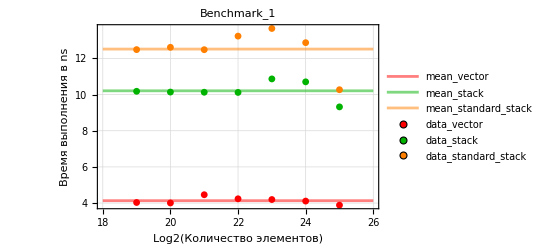

```mathematica
Block[{ meanV,meanS,meanSS},
meanV = Mean[#[[2]]/#[[1]]&/@dataVec1];meanS = Mean[#[[2]]/#[[1]]&/@dataStack1];meanSS = Mean[#[[2]]/#[[1]]&/@dataStandardStack1];
Show[
Plot[{meanV,meanS,meanSS},{x,18,26},PlotStyle->{Directive[Opacity[0.5],Red],RGBColor[0,0.7,0,0.5],Directive[Opacity[0.5],Orange]},PlotLegends->{{"mean_vector","mean_stack","mean_standard_stack"}},PlotTheme->"Detailed"],
ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@dataVec1,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Red,PlotLegends->{"data_vector"}],
ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@dataStack1,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->RGBColor[0,0.7,0,1],PlotLegends->{"data_stack"}],
ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@dataStandardStack1,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Orange,PlotLegends->{"data_standard_stack"}],
ImageSize->Scaled[0.8],PlotRange->Full,PlotRange->Full,PlotLabel->"Benchmark_1",FrameLabel->{"Log2(Количество элементов)", "Время выполнения в ns"}]
]
```

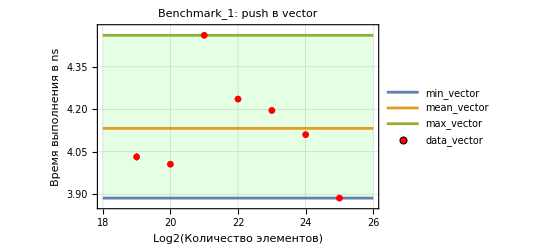

```mathematica
Block[{min, max, mean,data=dataVec1},
min = Min[#[[2]]/#[[1]]&/@data]; mean = Mean[#[[2]]/#[[1]]&/@data]; max=Max[#[[2]]/#[[1]]&/@data];
Show[Plot[{min,mean,max},{x,18,26},Filling->{1->{{3},Directive[Opacity[0.1],Green]}},PlotLegends->{"min_vector","mean_vector","max_vector"},PlotTheme->"Detailed"],ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@data,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Red,PlotLegends->{"data_vector"}],ImageSize->Scaled[0.8],PlotRange->{Automatic,{min-1/40,max+1/40}},PlotLabel->"Benchmark_1: push в vector",FrameLabel->{"Log2(Количество элементов)", "Время выполнения в ns"}]
]
```

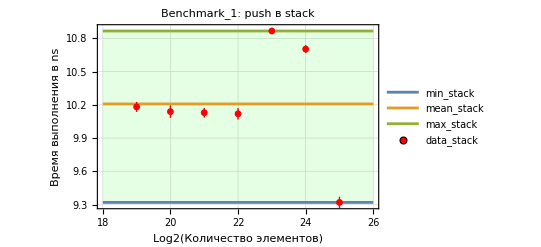

```mathematica
Block[{min, max, mean,data=dataStack1},
min = Min[#[[2]]/#[[1]]&/@data]; mean = Mean[#[[2]]/#[[1]]&/@data]; max=Max[#[[2]]/#[[1]]&/@data];
Show[Plot[{min,mean,max},{x,18,26},Filling->{1->{{3},Directive[Opacity[0.1],Green]}},PlotTheme->"Detailed",PlotLegends->{"min_stack","mean_stack","max_stack"}],ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@data,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Red,PlotLegends->{"data_stack"}],ImageSize->Scaled[0.8],PlotRange->{Automatic,{min-1/40,max+1/40}},PlotLabel->"Benchmark_1: push в stack",FrameLabel->{"Log2(Количество элементов)", "Время выполнения в ns"}]
]
```

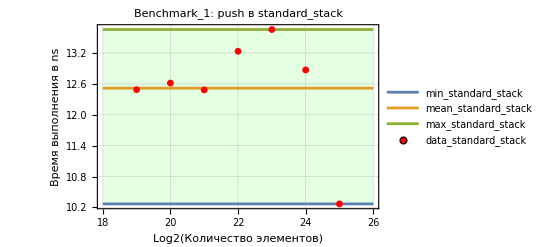

```mathematica
Block[{min, max, mean,data=dataStandardStack1},
min = Min[#[[2]]/#[[1]]&/@data]; mean = Mean[#[[2]]/#[[1]]&/@data]; max=Max[#[[2]]/#[[1]]&/@data];
Show[Plot[{min,mean,max},{x,18,26},Filling->{1->{{3},Directive[Opacity[0.1],Green]}},PlotLegends->{"min_standard_stack","mean_standard_stack","max_standard_stack"},PlotTheme->"Detailed"],ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@data,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Red,PlotLegends->{"data_standard_stack"}],ImageSize->Scaled[0.8],PlotRange->{Automatic,{min-1/40,max+1/40}},PlotLabel->"Benchmark_1: push в standard_stack",FrameLabel->{"Log2(Количество элементов)", "Время выполнения в ns"}]
]
```

### Benchmark 2: Push

```mathematica
dataVec2 ={{524288,2074950,5327},{1048576,4137699,1267},{2097152,8793185,2140},{4194304,17538595,4659},{8388608,34784486,121871},{16777216,68194411,299790},{33554432,129002061,356170}};
dataStack2 = {{524288,5749430,6212},{1048576,9931670,10149},{2097152,19867659,22779},{4194304,39873493,33449},{8388608,79811902,88185},{16777216,160400680,160228},{33554432,324034850,335074}};
dataStandardStack2 = {{524288,6427023,7683},{1048576,12737719,9832},{2097152,25263259,23628},{4194304,54163611,40388},{8388608,107818802,63779},{16777216,210718547,110252},{33554432,335895065,235322}};
```

```mathematica
lineVec2=Fit[{#[[1]],#[[2]]}&/@dataVec2,{1,x},x]
```

1.11411×10^6+3.85565 x

```mathematica
lineStack2=Fit[{#[[1]],#[[2]]}&/@dataStack2,{1,x},x]
```

-381135.+9.64694 x

```mathematica
lineStandardStack2=Fit[{#[[1]],#[[2]]}&/@dataStandardStack2,{1,x},x]
```

1.06229×10^7+10.1925 x

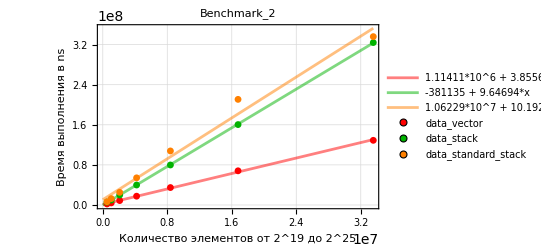

```mathematica
Show[
Plot[lineVec2,{x,0,dataVec2[[-1]][[1]]},PlotLegends->{"1.11411*10^6 + 3.85565*x"},PlotStyle->Directive[Opacity[0.5],Red],PlotTheme->"Detailed"],
Plot[lineStack2,{x,0,dataStack2[[-1]][[1]]},PlotLegends->{"-381135 + 9.64694*x"},PlotStyle->RGBColor[0,0.7,0,0.5]],
Plot[lineStandardStack2,{x,0,dataStandardStack2[[-1]][[1]]},PlotLegends->{"1.06229*10^7 + 10.1925*x"},PlotStyle->Directive[Opacity[0.5],Orange]],
ListPlot[{#[[1]],Around[#[[2]],#[[3]]]}&/@dataVec2,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Red,PlotLegends->{"data_vector"}],
ListPlot[{#[[1]],Around[#[[2]],#[[3]]]}&/@dataStack2,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->RGBColor[0,0.7,0,1],PlotLegends->{"data_stack"}],
ListPlot[{#[[1]],Around[#[[2]],#[[3]]]}&/@dataStandardStack2,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Orange,PlotLegends->{"data_standard_stack"}],ImageSize->Scaled[0.7],PlotRange->Full,PlotLabel->"Benchmark_2",FrameLabel->{"Количество элементов от 2^19 до 2^25", "Время выполнения в ns"}]
```

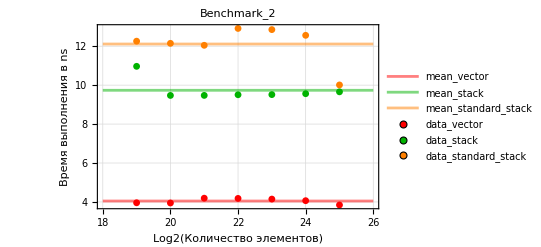

```mathematica
Block[{ meanV,meanS,meanSS},
meanV = Mean[#[[2]]/#[[1]]&/@dataVec2];meanS = Mean[#[[2]]/#[[1]]&/@dataStack2];meanSS = Mean[#[[2]]/#[[1]]&/@dataStandardStack2];
Show[
Plot[{meanV,meanS,meanSS},{x,18,26},PlotStyle->{Directive[Opacity[0.5],Red],RGBColor[0,0.7,0,0.5],Directive[Opacity[0.5],Orange]},PlotLegends->{{"mean_vector","mean_stack","mean_standard_stack"}},PlotTheme->"Detailed"],
ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@dataVec2,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Red,PlotLegends->{"data_vector"}],
ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@dataStack2,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->RGBColor[0,0.7,0,1],PlotLegends->{"data_stack"}],
ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@dataStandardStack2,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Orange,PlotLegends->{"data_standard_stack"}],
ImageSize->Scaled[0.8],PlotRange->Full,PlotLabel->"Benchmark_2",FrameLabel->{"Log2(Количество элементов)", "Время выполнения в ns"}]
]
```

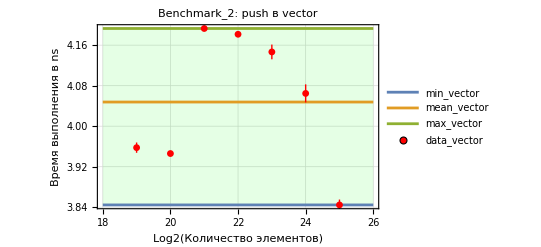

```mathematica
Block[{min, max, mean,data=dataVec2},
min = Min[#[[2]]/#[[1]]&/@data]; mean = Mean[#[[2]]/#[[1]]&/@data]; max=Max[#[[2]]/#[[1]]&/@data];
Show[Plot[{min,mean,max},{x,18,26},Filling->{1->{{3},Directive[Opacity[0.1],Green]}},PlotLegends->{"min_vector","mean_vector","max_vector"},PlotTheme->"Detailed"],ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@data,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Red,PlotLegends->{"data_vector"}],ImageSize->Scaled[0.8],PlotRange->{Automatic,{min-1/2000,max+1/2000}},PlotLabel->"Benchmark_2: push в vector",FrameLabel->{"Log2(Количество элементов)", "Время выполнения в ns"}]
]
```

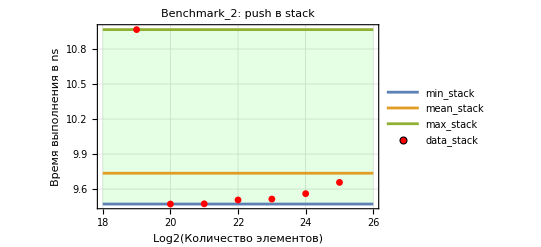

```mathematica
Block[{min, max, mean,data=dataStack2},
min = Min[#[[2]]/#[[1]]&/@data]; mean = Mean[#[[2]]/#[[1]]&/@data]; max=Max[#[[2]]/#[[1]]&/@data];
Show[Plot[{min,mean,max},{x,18,26},Filling->{1->{{3},Directive[Opacity[0.1],Green]}},PlotLegends->{"min_stack","mean_stack","max_stack"},PlotTheme->"Detailed"],ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@data,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Red,PlotLegends->{"data_stack"}],ImageSize->Scaled[0.8],PlotRange->Full,PlotLabel->"Benchmark_2: push в stack",FrameLabel->{"Log2(Количество элементов)", "Время выполнения в ns"}]
]
```

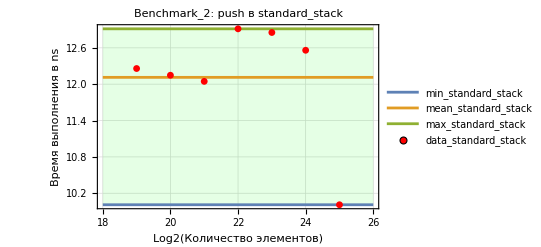

```mathematica
Block[{min, max, mean,data=dataStandardStack2},
min = Min[#[[2]]/#[[1]]&/@data]; mean = Mean[#[[2]]/#[[1]]&/@data]; max=Max[#[[2]]/#[[1]]&/@data];
Show[Plot[{min,mean,max},{x,18,26},Filling->{1->{{3},Directive[Opacity[0.1],Green]}},PlotLegends->{"min_standard_stack","mean_standard_stack","max_standard_stack"},PlotTheme->"Detailed"],ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@data,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Red,PlotLegends->{"data_standard_stack"}],ImageSize->Scaled[0.8],PlotRange->Full,PlotLabel->"Benchmark_2: push в standard_stack",FrameLabel->{"Log2(Количество элементов)", "Время выполнения в ns"}]
]
```

### Benchmark 3: back pop

```mathematica
dataVec3 ={{524288,354145,164/5},{1048576,707019,67},{2097152,1412826,807/10},{4194304,2824340,152},{8388608,5647231,402},{16777216,11292541,634}};
dataStack3 = {{524288,5367892,92390},{1048576,10740648,184308},{2097152,21490697,329977},{4194304,43849558,755933},{8388608,86478430,1535243},{16777216,173650902,3297541}};
dataStandardStack3 = {{524288,4425078,1608},{1048576,8978103,4250},{2097152,18101028,14111},{4194304,36339644,33367},{8388608,72683275,407056},{16777216,145740868,101814}};
```

```mathematica
lineVec3=Fit[{#[[1]],#[[2]]}&/@dataVec3,{1,x},x]
```

1407.89+0.673011 x

```mathematica
lineStack3=Fit[{#[[1]],#[[2]]}&/@dataStack3,{1,x},x]
```

-48250.2+10.3502 x

```mathematica
lineStandardStack3=Fit[{#[[1]],#[[2]]}&/@dataStandardStack3,{1,x},x]
```

-144321.+8.69309 x

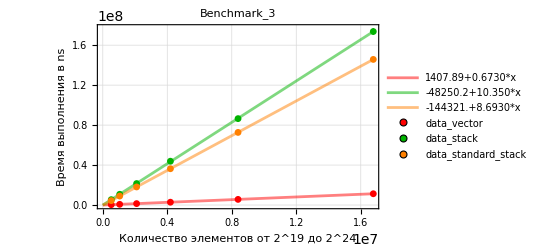

```mathematica
Show[
Plot[lineVec3,{x,0,dataVec3[[-1]][[1]]},PlotLegends->{"1407.89+0.6730*x"},PlotStyle->Directive[Opacity[0.5],Red],PlotTheme->"Detailed"],
Plot[lineStack3,{x,0,dataStack3[[-1]][[1]]},PlotLegends->{"-48250.2+10.350*x"},PlotStyle->RGBColor[0,0.7,0,0.5]],
Plot[lineStandardStack3,{x,0,dataStandardStack3[[-1]][[1]]},PlotLegends->{"-144321.+8.6930*x"},PlotStyle->Directive[Opacity[0.5],Orange]],
ListPlot[{#[[1]],Around[#[[2]],#[[3]]]}&/@dataVec3,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Red,PlotLegends->{"data_vector"}],
ListPlot[{#[[1]],Around[#[[2]],#[[3]]]}&/@dataStack3,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->RGBColor[0,0.7,0,1],PlotLegends->{"data_stack"}],
ListPlot[{#[[1]],Around[#[[2]],#[[3]]]}&/@dataStandardStack3,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Orange,PlotLegends->{"data_standard_stack"}],ImageSize->Scaled[0.8],PlotRange->Full,PlotLabel->"Benchmark_3",FrameLabel->{"Количество элементов от 2^19 до 2^24", "Время выполнения в ns"}]
```

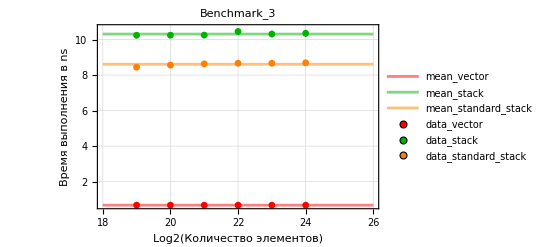

```mathematica
Block[{ meanV,meanS,meanSS},
meanV = Mean[#[[2]]/#[[1]]&/@dataVec3];meanS = Mean[#[[2]]/#[[1]]&/@dataStack3];meanSS = Mean[#[[2]]/#[[1]]&/@dataStandardStack3];
Show[
Plot[{meanV,meanS,meanSS},{x,18,26},PlotStyle->{Directive[Opacity[0.5],Red],RGBColor[0,0.7,0,0.5],Directive[Opacity[0.5],Orange]},PlotLegends->{{"mean_vector","mean_stack","mean_standard_stack"}},PlotTheme->"Detailed"],
ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@dataVec3,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Red,PlotLegends->{"data_vector"}],
ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@dataStack3,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->RGBColor[0,0.7,0,1],PlotLegends->{"data_stack"}],
ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@dataStandardStack3,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Orange,PlotLegends->{"data_standard_stack"}],
ImageSize->Scaled[0.8],PlotRange->Full,PlotLabel->"Benchmark_3",FrameLabel->{"Log2(Количество элементов)", "Время выполнения в ns"}]
]
```

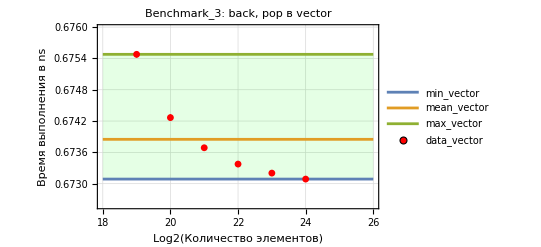

```mathematica
Block[{min, max, mean,data=dataVec3},
min = Min[#[[2]]/#[[1]]&/@data]; mean = Mean[#[[2]]/#[[1]]&/@data]; max=Max[#[[2]]/#[[1]]&/@data];
Show[Plot[{min,mean,max},{x,18,26},Filling->{1->{{3},Directive[Opacity[0.1],Green]}},PlotLegends->{"min_vector","mean_vector","max_vector"},PlotTheme->"Detailed"],ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@data,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Red,PlotLegends->{"data_vector"}],ImageSize->Scaled[0.8],PlotRange->{Automatic,{min-1/2000,max+1/2000}},PlotLabel->"Benchmark_3: back, pop в vector",FrameLabel->{"Log2(Количество элементов)", "Время выполнения в ns"}]
]
```

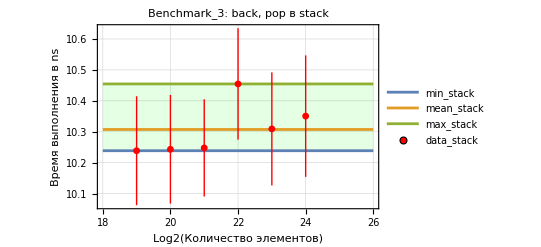

```mathematica
Block[{min, max, mean,data=dataStack3},
min = Min[#[[2]]/#[[1]]&/@data]; mean = Mean[#[[2]]/#[[1]]&/@data]; max=Max[#[[2]]/#[[1]]&/@data];
Show[Plot[{min,mean,max},{x,18,26},Filling->{1->{{3},Directive[Opacity[0.1],Green]}},PlotLegends->{"min_stack","mean_stack","max_stack"},PlotTheme->"Detailed"],ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@data,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Red,PlotLegends->{"data_stack"}],ImageSize->Scaled[0.8],PlotRange->Full,PlotLabel->"Benchmark_3: back, pop в stack",FrameLabel->{"Log2(Количество элементов)", "Время выполнения в ns"}]
]
```

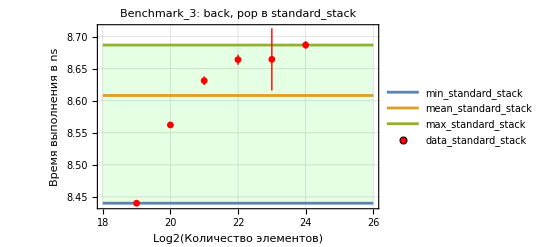

```mathematica
Block[{min, max, mean,data=dataStandardStack3},
min = Min[#[[2]]/#[[1]]&/@data]; mean = Mean[#[[2]]/#[[1]]&/@data]; max=Max[#[[2]]/#[[1]]&/@data];
Show[Plot[{min,mean,max},{x,18,26},Filling->{1->{{3},Directive[Opacity[0.1],Green]}},PlotLegends->{"min_standard_stack","mean_standard_stack","max_standard_stack"},PlotTheme->"Detailed"],ListPlot[{Log2[#[[1]]],Around[#[[2]],#[[3]]]/#[[1]]}&/@data,PlotMarkers->Graphics[{Disk[]},ImageSize->7],PlotStyle->Red,PlotLegends->{"data_standard_stack"}],ImageSize->Scaled[0.8],PlotRange->Full,PlotLabel->"Benchmark_3: back, pop в standard_stack",FrameLabel->{"Log2(Количество элементов)", "Время выполнения в ns"}]
]
```